```mathematica
(* Que: Maximize 2x+y
s.t. x+2y≤12
	 x+2.3y≤6.9
	 x+1.4y≤4.9
	  x≥0, y≥0
*)

Maximize[{ 2 x+y, x+2y≤12 && x+2.3 y≤6.9 && x+1.4 y≤4.9 && x≥0,y≥0},{x,y}]
```

{9.8,{x→4.9,y→0.}}

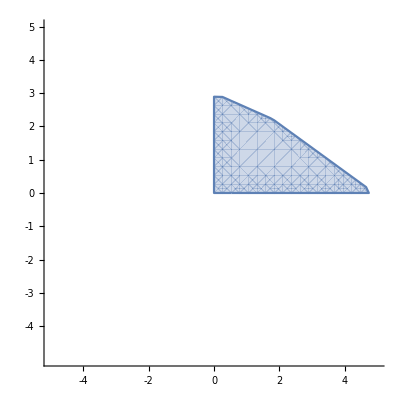

```mathematica
RegionPlot[{x+2 y≤12 && x+2.3 y≤6.9 && x+1.4 y≤4.9 && x≥0 && y≥0},{x,-5,5},{y,-5,5},Frame->False,Axes->True,Ticks->{{-4,-3,-2,-1,0,1,2,3,4,5},{-4,-3,-2,-1,0,1,2,3,4,5}}]
```

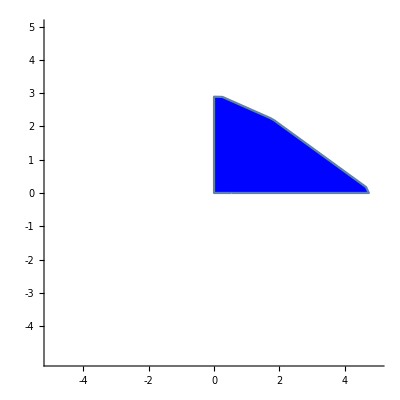

```mathematica
RegionPlot[{x+2 y≤12 && x+2.3 y≤6.9 && x+1.4 y≤4.9 && x≥0 && y≥0},{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0., 0.01, 1.], Frame->False,Axes->True,Ticks->{{-4,-3,-2,-1,0,1,2,3,4,5},{-4,-3,-2,-1,0,1,2,3,4,5}}]
```